```mathematica
G := 6.67*10^-8
Mstar := 1.4 * (2*10^33)
rstar := 10^6
gz = G * Mstar/rstar^2
me := 9.109 * 10 ^ -28
mp := 1.672*10^-24
c:=3*10^10
mu := 2
h:=6.626*10^-27
k := 1/(me*c)  * (3*h^3/(8*Pi*mu*mp))^(1/3)
c1:= Pi/3*me^4*c^5/h^3 * 8/5
xf[r_]:= k * r ^ (1/3)
p[r_]= c1* xf[r]^5/Sqrt[1+16/25*xf[r]^2]
```

1.8676×10^14

(3.12516×10^12 r^(5/3))/(√(1+0.0000407921 r^(2/3)))

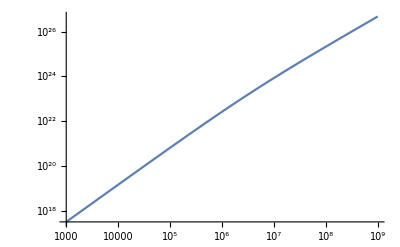

```mathematica
LogLogPlot[p[r],{r,10^3, 10^9}]
```

```mathematica
a[r_] = D[p[r],r]
```

(5.2086×10^12 r^(2/3))/(√(1+0.0000407921 r^(2/3)))-(4.24939×10^7 r^(4/3))/((1+0.0000407921 r^(2/3))^(3/2))

```mathematica
rhoc := 10^9

 sol = NDSolve[{a[rho[z]] * 1/rho[z] * rho'[z] == -gz, rho[0]==rhoc},rho[z],{z, 0, 9313}]
```

{{rho[z]→InterpolatingFunction[…][z]}}

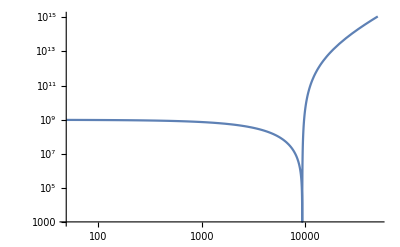

```mathematica
LogLogPlot[Evaluate[rho[z]/.sol], {z, 0, 50000},PlotRange->All]
```

```mathematica
Integrate[Evaluate[rho[z]/.sol],{z,10,15}]
```

{4.98202×10^9}

```mathematica
data = Flatten[Table[{z,rho[z]/.sol},{z,0,9313, 1}]]
Export["/Users/cristozilleruelo/Desktop/UvA/Astrovaria/astrovaria_ns_atmosphere/data/Paczynski.csv",data,"CSV"]
```

{0,1.×10^9,1,9.99712×10^8,2,9.99424×10^8,3,9.99136×10^8,4,9.98848×10^8,5,18606,1538.98,9309,1142.87,9310,788.375,9311,480.96,9312,229.168,9313,49.7525}
 |  |  |  |

/Users/cristozilleruelo/Desktop/UvA/Astrovaria/astrovaria_ns_atmosphere/data/Paczynski.csv

```mathematica
Directory[]
```

/Users/cristozilleruelo

```mathematica
Clear[rho2]
p2[r_] := 3.12*10^12 * r ^(5/3)
a2[r_] :=  D[p2[r],r]
DSolve[{a2[rho2[z]] * 1/rho2[z]*rho2'[z]==-gz, rho2[0]==10^9}, rho2[z], z]
Clear[rho22]
```

{{rho2[z]→117.161 (41764.8-1. z)^(3/2)}}

117.161 (41764.8-1. z)^(3/2)

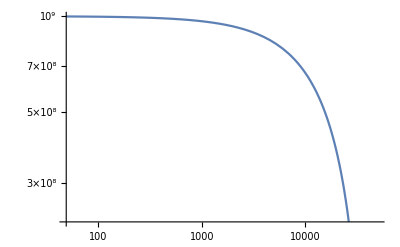

{{z→41764.8}}

```mathematica
rho2[z] = 117.16122229579658 (41764.83186977941-1. z)^(3/2)
LogLogPlot[rho2[z], {z, 0, 50000}]
Solve[rho2[z]==0, z]
```

```mathematica
Clear[rho2]
rhochange = 4037017.258596558
Solve[rho3[z]==rhochange, z]
DSolve[{a2[rho2[z]] * 1/rho2[z] * rho2'[z] == -gz, rho2[8805.6836882763]==rhochange},rho2[z],z]
```

4.03702×10^6

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→rho3^(-1)[4.03702×10^6]}}

{{rho2[z]→117.161 (9864.57-1. z)^(3/2)}}

```mathematica
rho2[z_]=117.16122229579658 (9864.57440646902-1. z)^(3/2)
```

117.161 (9864.57-1. z)^(3/2)

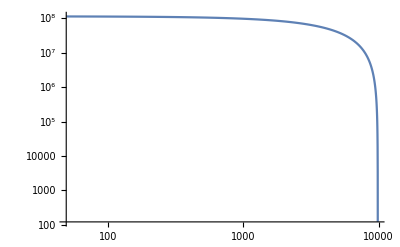

```mathematica
LogLogPlot[rho2[z],{z,0,50000}, PlotRange->All]
```

```mathematica
p3[r_] = 4.89*10^14 * r ^(4/3)
a3[r_] =  D[p3[r],r]
```

4.89×10^14 r^(4/3)

6.52×10^14 r^(1/3)

```mathematica
zchange = 40705.9
Clear[rho3]
DSolve[{a3[rho3[z]] * 1/rho3[z] * rho3'[z] == -gz, rho3[0]==10^9},rho3[z],z]
```

40705.9

{{rho3[z]→-0.000870452 (-1.14883×10^12+3.29072×10^8 z-31420. z^2+1. z^3)},{rho3[z]→-0.000870452 ((-1.14883×10^12-0.000162312 ⅈ)-(1.64536×10^8+2.84985×10^8 ⅈ) z+(15710.-27210.5 ⅈ) z^2+1. z^3)},{rho3[z]→-0.000870452 ((-1.14883×10^12+0.000162312 ⅈ)-(1.64536×10^8-2.84985×10^8 ⅈ) z+(15710.+27210.5 ⅈ) z^2+1. z^3)}}

-0.000870452 (-1.14883×10^12+3.29072×10^8 z-31420. z^2+1. z^3)

{{z→10473.3},{z→10473.3},{z→10473.3}}

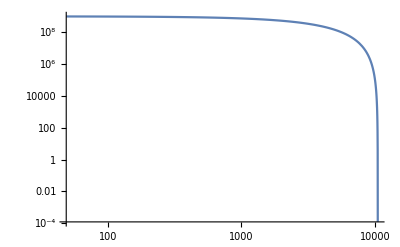

```mathematica
rho3[z_]= -0.0008704524348117549 (-1.1488278509052148*^12+3.2907222305990475*^8 z-31420.0042835725 z^2+1. z^3)
Solve[rho3[z]==0, z]
LogLogPlot[rho3[z],{z,0,50000}, PlotRange->All]
```

```mathematica
PacData=Flatten[Table[{path, Integrate[Evaluate[rho[z]/.sol],{z, 9313,path }]},{path, 0, 9313, 1}], 1]
```

{0,{-2.58846×10^12},1,{-2.58746×10^12},2,{-2.58646×10^12},3,{-2.58546×10^12},4,{-2.58446×10^12},18608,9309,{-2074.58},9310,{-1112.63},9311,{-482.172},9312,{-132.24},9313,{0}}
 |  |  |  |

```mathematica
Export["/Users/cristozilleruelo/Desktop/UvA/Astrovaria/astrovaria_ns_atmosphere/data/Paczynski_column.csv",PacData,"CSV"]
```

/Users/cristozilleruelo/Desktop/UvA/Astrovaria/astrovaria_ns_atmosphere/data/Paczynski_column.csv

```mathematica
Integrate[Evaluate[rho[z]/.sol],{z, 9313, 0}]
```

{-2.58846×10^12}

```mathematica
combined = Piecewise[{{rho2[z], z<8805.68},{rho3[z], z≥8805.68}}]
```

Piecewise[{{117.161 (9864.57-1. z)^(3/2), z<8805.68}, {-0.000870452 (-1.14883×10^12+3.29072×10^8 z-31420. z^2+1. z^3), z≥8805.68}, {0, True}}]

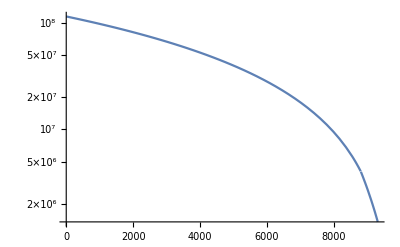

```mathematica
LogPlot[combined, {z, 0, 9313}]
```

```mathematica
combinedData = Table[zi, Integrate[combined, {z, 9313, zi}], {zi, 0, 9313, 1000}]
```

Integrate::pwrl: Unable to prove that integration limits {9313,zi} are real. Adding assumptions may help.

Table::nliter: Non-list iterator ∫_9313^zi combinedⅆz at position 2 does not evaluate to a real numeric value.

Table[zi,∫_9313^zi combinedⅆz,{zi,0,9313,1000}]

```mathematica
Integrate[combined, {z, 9313, 9313}]
```

0

```mathematica
NRData =  Table[path, Integrate[rho3[z], {z, 9313, path}], {path, 8808.68,  9313, 1}]
```

Table::nliter: Non-list iterator ∫_9313^path rho3[z]ⅆz at position 2 does not evaluate to a real numeric value.

```mathematica
Table[path,∫_9313^path rho3[z]ⅆz,{path,8809,9312,1}]
```

Table::nliter: Non-list iterator ∫_9313^path rho3[z]ⅆz at position 2 does not evaluate to a real numeric value.

Table[path,∫_9313^path rho3[z]ⅆz,{path,8809,9312,1}]

```mathematica
Integrate[rho3[z], {z, 9313, 8808.68}]
```

-1.27655×10^9

```mathematica
Solve[rho3[z]==0, z]
```

{{z→10473.3},{z→10473.3},{z→10473.3}}